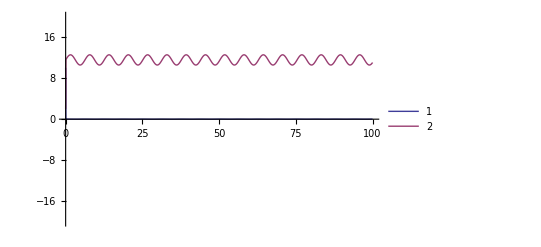

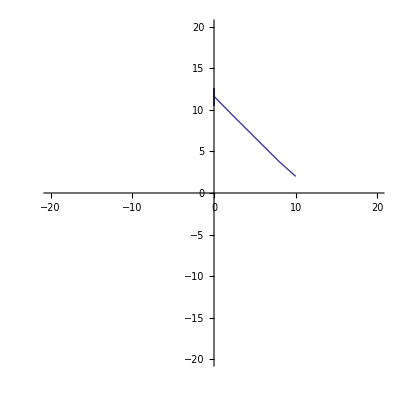

```mathematica
tmax = 100;
ymax=20;
s=NDSolve[{x'[t]==Cos[t]-x[t]y[t]^2, y'[t]==x[t]y[t]^2 - x[t],y[0]==2,x[0]==10},{x,y},{t,0,tmax}];
Plot[Evaluate[{x[t],y[t]}/.s],{t,0,tmax}, PlotRange->{{0, tmax},{-ymax, ymax}}, PlotLegends->{1, 2}]
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,tmax}, PlotRange->{-ymax,ymax}]
```